```mathematica
Clear["Global`*"]
```

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]];
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
im1 = y μ-2 x y μ;
```

```mathematica
im = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
```

Abaixo, temos os valores que y precisa assumir para que na terceira iteração do mapa logístico complexo, a parte imaginária seja nula. Percebemos que esses valores são funções de x e de μ.

```mathematica
ys1 = FullSimplify[ Solve[im1==0,y]]
```

{}

```mathematica
ys =FullSimplify[ Solve[im==0,y]]
```

{{y→0},{y→-(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→-(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→-(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)}}

Refazendo o mesmo procedimento para x, encontramos 6 funções que são equivalentes às 6 últimas da célula anterior, com exceção da primeira que, apesar de ser trivial, não havia sido fornecida anteriormente.

```mathematica
xs = Solve[im==0,x]
```

{{x→1/2},{x→(μ-√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ)},{x→(μ+√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ)},{x→1/2 (1-√(1+12 y^2-2/μ-(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1+√(1+12 y^2-2/μ-(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1-√(1+12 y^2-2/μ+(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1+√(1+12 y^2-2/μ+(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))}}

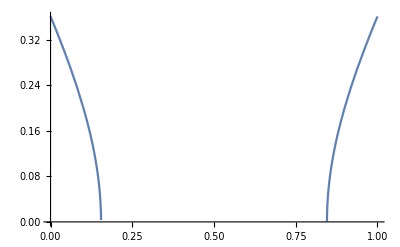

```mathematica
Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,0,1}]
```

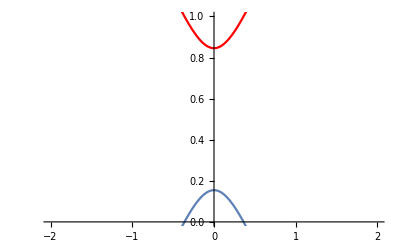

```mathematica
Show[Plot[xs⟦2,1,2⟧/.μ-> 3.8284,{y,-1,1}],Plot[xs⟦3,1,2⟧/.μ-> 3.8284,{y,-1,1},PlotStyle->Red],PlotRange-> {{-2,2},{0,1}}]
```

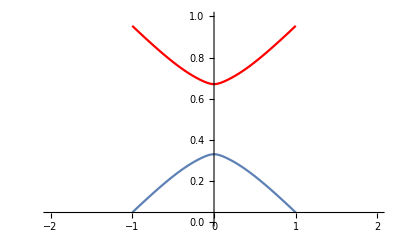

```mathematica
Show[Plot[xs⟦4,1,2⟧/.μ-> 3.8284,{y,-1,1}],Plot[xs⟦5,1,2⟧/.μ-> 3.8284,{y,-1,1},PlotStyle->Red],PlotRange-> {{-2,2},{0,1}}]
```

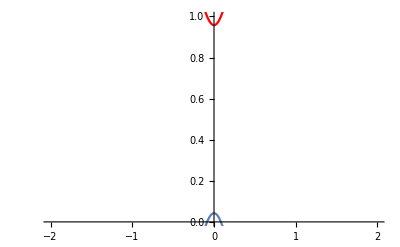

```mathematica
Show[Plot[xs⟦6,1,2⟧/.μ-> 3.8284,{y,-1,1}],Plot[xs⟦7,1,2⟧/.μ-> 3.8284,{y,-1,1},PlotStyle->Red],PlotRange-> {{-2,2},{0,1}}]
```

Então, no plano xy, encontramos os valores para os quais a componente imaginária será nula na terceira iteração.

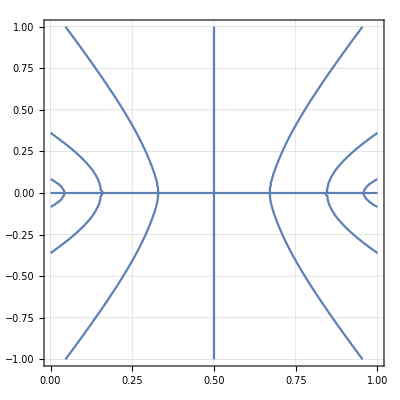

```mathematica
imμ =im/.μ-> 3.8284;
ContourPlot[imμ== 0,{x,0,1},{y,-1,1},GridLines->Automatic]
```

```mathematica
x0s = xs/.{y-> 0, μ-> 3.8284}
```

{{x→1/2},{x→0.154461},{x→0.845539},{x→0.329294},{x→0.670706},{x→0.0421202},{x→0.95788}}

Agora, nos deparamos com a seguinte pergunta:
Como se comportam os valores PRÓXIMOS das curvas de estabilidade que encontramos anteriormente? Podemos pensar em uma pequena variação ϵ com relação aos valores originais, e exigir que:

|y_im/y_s|< 1 , sendo:
y_im = componente imaginária da terceira iteração
     y_s = valor para o qual a componente imaginária da terceira iteração é 0

```mathematica
banda1= FullSimplify[Normal[Series[im/y,{x,1/2,8}]/.μ-> 3.8284]/.x-> 1/2+ϵ];
```

```mathematica
bandaN= FullSimplify[im/y/.x-> (x+ ϵ)/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
bandaN
```

-56.1115 (-1+2 x0+2 ϵ) (1+7.6568 (x0^2-y^2+(-1+ϵ) ϵ+x0 (-1+2 ϵ))) (1+29.3133 (-x0+x0^2-y^2-ϵ+2 x0 ϵ+ϵ^2+3.8284 (x0^2+y-y^2-2 y ϵ+(-1+ϵ) ϵ+x0 (-1-2 y+2 ϵ)) (x0^2-y (1+y)+(-1+2 y) ϵ+ϵ^2+x0 (-1+2 y+2 ϵ))))

```mathematica
banda2= FullSimplify[im/ys⟦2,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦2,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda3= FullSimplify[im/ys⟦3,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda4= FullSimplify[im/ys⟦4,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦4,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda5= FullSimplify[im/ys⟦5,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦5,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda6= FullSimplify[im/ys⟦6,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦6,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
banda7= FullSimplify[im/ys⟦7,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦7,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

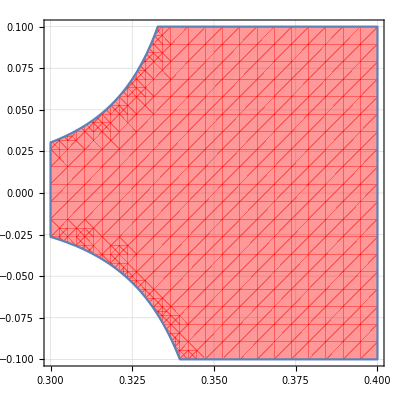

```mathematica
bandaseries = Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]];
banda2series= FullSimplify[bandaseries/ys⟦2,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦2,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
RegionPlot[Abs[banda2series]< 1,{x0,0.3,0.4},{ϵ,-0.1,0.1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4],MaxRecursion->5}]
```

```mathematica
RegionPlot[Abs[banda1]< 1,{x0,0.3,0.4},{ϵ,-0.1,0.1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4],MaxRecursion->5}]
```

-Graphics-

```mathematica
ϵlist = FullSimplify[Solve[Abs[banda2series]== 1,ϵ]];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϵ→(0.5 (-1.72738×10^94+3.45476×10^94 x0-1. √(9.11093×10^194-4.12346×10^196 x0+8.49192×10^197 x0^2-1.05663×10^199 x0^3+8.89648×10^199 x0^4-5.37942×10^200 x0^5+2.41914×10^201 x0^6-8.26332×10^201 x0^7+2.16949×10^202 x0^8-4.39804×10^202 x0^9+6.86967×10^202 x0^10-8.19019×10^202 x0^11+7.31419×10^202 x0^12-4.73458×10^202 x0^13+2.09695×10^202 x0^14-5.68233×10^201 x0^15+7.10292×10^200 x0^16)))/(1.00963×10^101-3.79638×10^102 x0+6.42623×10^103 x0^2-6.49798×10^104 x0^3+4.39125×10^105 x0^4-2.1014×10^106 x0^5+7.35548×10^106 x0^6-1.91609×10^107 x0^7+3.73825×10^107 x0^8-5.44285×10^107 x0^9+5.82863×10^107 x0^10-4.45643×10^107 x0^11+2.30186×10^107 x0^12-7.19594×10^106 x0^13+1.02799×10^106 x0^14)},{ϵ→(0.5 (-1.72738×10^94+3.45476×10^94 x0+√(9.11093×10^194-4.12346×10^196 x0+8.49192×10^197 x0^2-1.05663×10^199 x0^3+8.89648×10^199 x0^4-5.37942×10^200 x0^5+2.41914×10^201 x0^6-8.26332×10^201 x0^7+2.16949×10^202 x0^8-4.39804×10^202 x0^9+6.86967×10^202 x0^10-8.19019×10^202 x0^11+7.31419×10^202 x0^12-4.73458×10^202 x0^13+2.09695×10^202 x0^14-5.68233×10^201 x0^15+7.10292×10^200 x0^16)))/(1.00963×10^101-3.79638×10^102 x0+6.42623×10^103 x0^2-6.49798×10^104 x0^3+4.39125×10^105 x0^4-2.1014×10^106 x0^5+7.35548×10^106 x0^6-1.91609×10^107 x0^7+3.73825×10^107 x0^8-5.44285×10^107 x0^9+5.82863×10^107 x0^10-4.45643×10^107 x0^11+2.30186×10^107 x0^12-7.19594×10^106 x0^13+1.02799×10^106 x0^14)}}

```mathematica
ϵlist⟦1,1,2⟧
```

(-8.63689×10^93+1.72738×10^94 x0-0.5 √(9.11093×10^194+x0 (-4.12346×10^196+x0 (8.49192×10^197+x0 (-1.05663×10^199+x0 (8.89648×10^199+x0 (-5.37942×10^200+x0 (2.41914×10^201+x0 (-8.26332×10^201+x0 (2.16949×10^202+x0 (-4.39804×10^202+x0 (6.86967×10^202+x0 (-8.19019×10^202+x0 (7.31419×10^202+x0 (-4.73458×10^202+x0 (2.09695×10^202+x0 (-5.68233×10^201+7.10292×10^200 x0)))))))))))))))))/(1.00963×10^101+x0 (-3.79638×10^102+x0 (6.42623×10^103+x0 (-6.49798×10^104+x0 (4.39125×10^105+x0 (-2.1014×10^106+x0 (7.35548×10^106+x0 (-1.91609×10^107+x0 (3.73825×10^107+x0 (-5.44285×10^107+x0 (5.82863×10^107+x0 (-4.45643×10^107+x0 (2.30186×10^107+x0 (-7.19594×10^106+1.02799×10^106 x0))))))))))))))

Atenção ao fato de que cada solução de ϵlist apresenta um comportamento diferente (banana ideal, banana invertida).

(0.-0.36139 ⅈ) √(-1-7.6568 (-1+x0) x0)

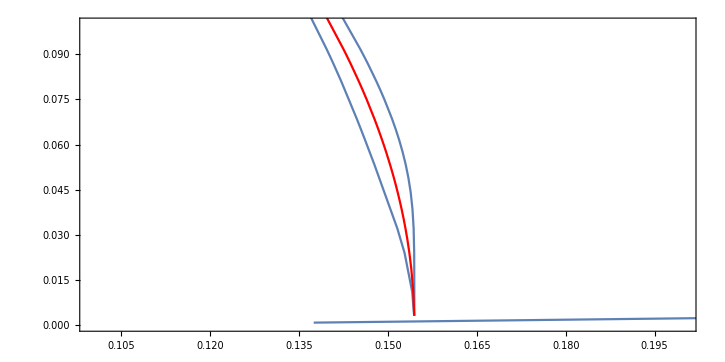

```mathematica
lixo = ys⟦2,1,2⟧/.{μ-> 3.8284,x-> x0}
Show[ParametricPlot[{x0+ ϵlist⟦2,1,2⟧, lixo},{x0,0,1},PlotRange->{{0.10,0.20},{0,0.1}},Frame->True,MaxRecursion->5],
ParametricPlot[{x0- ϵlist⟦2,1,2⟧, lixo},{x0,0,1},PlotRange->{{0,1},{0,0.1}},Frame->True,MaxRecursion->5],
Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,0,1},PlotStyle->Red],AspectRatio-> 1/2]
```

```mathematica
banda2series= FullSimplify[bandaseries/ys⟦2,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦2,1,2⟧}/.x-> x0 ]/.μ-> 3.8284
```

(214.817 (1-2 x0)^2 √(-1-7.6568 (-1+x0) x0) (-2+3.8284 (1+7.6568 x0 (-1+2 x0)) (1+3.8284 (2-6 x0+4 x0^2))) ϵ)/(√(-1-7.6568 (-1+x0+ϵ) (x0+ϵ)))

```mathematica
FullSimplify[banda2 - banda2series]
```

1/(√(-1-7.6568 (-1.+x0+ϵ) (x0+ϵ)))2.70003×10^6 √(-1-7.6568 (-1.+x0) x0) ϵ (-3.36846×10^-19+ϵ (-0.0167618+x0 (0.223825+x0 (-1.0709+x0 (2.3806+x0 (-2.5+1. x0))))+0.0244133 ϵ+x0 (-0.346489+x0 (1.34649+x0 (-2.+1. x0))) ϵ+(0.0426418-0.0852837 x0) ϵ^2+(-0.142057+(0.5-0.5 x0) x0) ϵ^3+(0.125-0.25 x0) ϵ^4-0.0357143 ϵ^5))

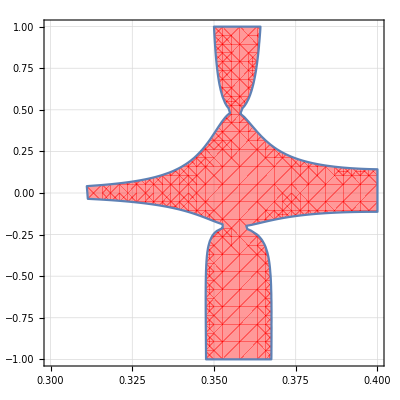

```mathematica
RegionPlot[Abs[banda2series]< 1,{x0,0.3,0.4},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4]}]
```

```mathematica
Clear["Global`*"]
```

```mathematica
z = R Sin[θ] ⅈ + R Cos[θ]+0.5;
circularmap[] = z μ (1 - z)
circularmap[circularmap[circularmap[z]]]
```

μ (0.5-R Cos[θ]-ⅈ R Sin[θ]) (0.5+R Cos[θ]+ⅈ R Sin[θ])

μ (1-R Cos[θ]-ⅈ R Sin[θ]) (R Cos[θ]+ⅈ R Sin[θ])

```mathematica
circularmap[μ (1-R Cos[θ]-ⅈ R Sin[θ]) (R Cos[θ]+ⅈ R Sin[θ])]
```

μ (1-R Cos[θ]-ⅈ R Sin[θ]) (R Cos[θ]+ⅈ R Sin[θ])

```mathematica
Assuming[{R>0,μ>0, θ>0},ComplexExpand[μ (0.5-R Cos[θ]-ⅈ R Sin[θ]) (0.5+R Cos[θ]+ⅈ R Sin[θ]), TargetFunctions->{Abs, Arg}]]
```

0.+0.25 μ-R^2 μ Cos[θ]^2+R^2 μ Sin[θ]^2+ⅈ (0.-2 R^2 μ Cos[θ] Sin[θ])

```mathematica
FullSimplify[ArcTan[(R μ Sin[θ]-2 R^2 μ Cos[θ] Sin[θ])/(R μ Cos[θ]-R^2 μ Cos[θ]^2+R^2 μ Sin[θ]^2)]/.R-> 1/2]
```

-ArcTan[(2 (-1+Cos[θ]) Sin[θ])/(2 Cos[θ]-Cos[2 θ])]

```mathematica
FullSimplify[(2 (-1+Cos[θ]) Sin[θ])/(2 Cos[θ]-Cos[2 θ])]
```

(2 (-1+Cos[θ]) Sin[θ])/(2 Cos[θ]-Cos[2 θ])

```mathematica
TeXForm[(2 (-1+Cos[θ]) Sin[θ])/(2 Cos[θ]-Cos[2 θ])]
```

\frac{2 \sin (\theta ) (\cos (\theta )-1)}{2 \cos (\theta )-\cos (2 \theta )}

```mathematica
FullSimplify[√((R μ Sin[θ]-2 R^2 μ Cos[θ] Sin[θ])^2+(R μ Cos[θ]-R^2 μ Cos[θ]^2+R^2 μ Sin[θ]^2)^2)]
```

√(R^2 μ^2 (1+R^2-2 R Cos[θ]))

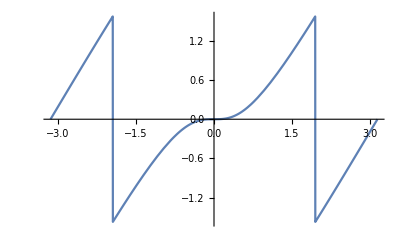

```mathematica
Plot[ArcTan[((-1+2 R Cos[θ]) Sin[θ])/(-Cos[θ]+R Cos[2 θ])]/.R-> 0.5, {θ,-π, π}]
```

```mathematica
Abs[ⅇ^(ⅈ θ)/. θ-> π/2]
```

1

```mathematica
μ = 3.8284;
listcircle = {};
For[R = 0, R<0.5,R+=0.01;
localcircle={};
For[θ=0, θ<2 Pi, θ+=0.001;
x = Abs[Im[R ⅇ^(ⅈ θ)]]+0.5;
y = Re[R ⅇ^(ⅈ θ)];
AppendTo[localcircle,{x,y}]];
AppendTo[listcircle, localcircle]]
```

```mathematica
μ = 3.8284;
listcircle = {};
For[R = 0, R<0.5,R+=0.01;
localcircle={};
For[θ=0, θ<2 Pi, θ+=0.001;
x = R Sin[θ]+0.5;
y = R Cos[θ];
AppendTo[localcircle,{x,y}]];
AppendTo[listcircle, localcircle]]
```

```mathematica
circlemap0={};
For[i=0,i<Length[listcircle],i++;
localcircle=ListPlot[listcircle⟦i⟧,PlotStyle->Hue[i/(1.15Length[listcircle])]];
AppendTo[circlemap0,localcircle]];
```

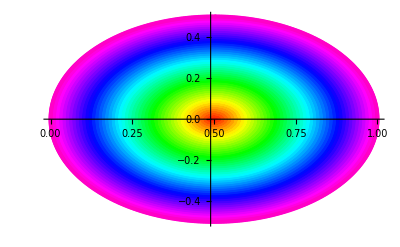

```mathematica
Show[circlemap0,PlotRange->All]
```

```mathematica
colourplotcircle={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] = x μ-x^2 μ+y^2 μ;
yn[x_,y_] = y μ-2 x y μ;
For[m=0,m<Length[listcircle],m++;
locallistcircle = {};
For[n=0,n<Length[listcircle⟦m⟧],n++;
xlocal = listcircle⟦m,n,1⟧;
ylocal = listcircle⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[locallistcircle,{x1,y1}]];
AppendTo[colourplotcircle,locallistcircle]]
```

```mathematica
circlemap1={};
For[i=0,i<Length[colourplotcircle],i++;
localcircle=ListPlot[colourplotcircle⟦i⟧,PlotStyle->Hue[i/(1.15Length[colourplotcircle])]];
AppendTo[circlemap1,localcircle]];
```

```mathematica
Show[circlemap1,PlotRange-> {{0.955,0.96},{-0.001,0.001}}]
```

-Graphics-

```mathematica
colourplotcircle2={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] =x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
yn[x_,y_] = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
For[m=0,m<Length[listcircle],m++;
locallistcircle = {};
For[n=0,n<Length[listcircle⟦m⟧],n++;
xlocal = listcircle⟦m,n,1⟧;
ylocal = listcircle⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[locallistcircle,{x1,y1}]];
AppendTo[colourplotcircle2,locallistcircle]]
```

```mathematica
circlemap2={};
For[i=0,i<Length[colourplotcircle2],i++;
localcircle=ListPlot[colourplotcircle2⟦i⟧,PlotStyle->Hue[i/(1.15Length[colourplotcircle2])]];
AppendTo[circlemap2,localcircle]];
```

```mathematica
colourplotcircle3={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] = x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7;
yn[x_,y_] = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
For[m=0,m<Length[listcircle],m++;
locallistcircle = {};
For[n=0,n<Length[listcircle⟦m⟧],n++;
xlocal = listcircle⟦m,n,1⟧;
ylocal = listcircle⟦m,n,2⟧;
{x3 ,y3}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[locallistcircle,{x3,y3}]];
AppendTo[colourplotcircle3,locallistcircle]]
```

```mathematica
circlemap3={};
For[i=0,i<Length[colourplotcircle3],i++;
localcircle=ListPlot[colourplotcircle3⟦i⟧,PlotStyle->Hue[i/(1.15Length[colourplotcircle3])]];
AppendTo[circlemap3,localcircle]];
```

```mathematica
Show[circlemap0,PlotRange-> {{0,1},{-0.1,0.1}}, Frame-> True, GridLines-> Automatic]
```

-Graphics-

```mathematica
Show[circlemap3,PlotRange-> {{0,1},{-0.1,0.1}}, Frame-> True,GridLines-> Automatic]
```

-Graphics-

```mathematica
circlemap0={};
For[i=0,i<Length[listcircle],i++;
localcircle={};
For[j=0,j<Length[listcircle⟦i⟧], j++;
pointcircle=ListPlot[{listcircle⟦i,j⟧},PlotStyle->{Hue[i/(1.15Length[listcircle])],Opacity[0.05+j/(2.25Length[listcircle⟦i⟧])]}];
AppendTo[localcircle,pointcircle]];
AppendTo[circlemap0,localcircle]];
```

```mathematica
circlemap1={};
For[i=0,i<Length[colourplotcircle],i++;
localcircle={};
For[j=0,j<Length[colourplotcircle⟦i⟧], j++;
pointcircle=ListPlot[{colourplotcircle⟦i,j⟧},PlotStyle->{Hue[i/(1.15Length[colourplotcircle])],Opacity[0.05+j/(2.25Length[colourplotcircle⟦i⟧])]}];
AppendTo[localcircle,pointcircle]];
AppendTo[circlemap1,localcircle]];
```

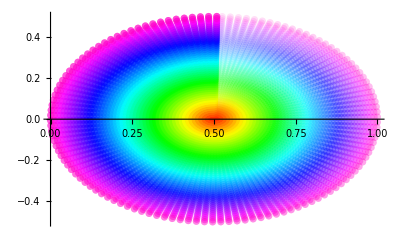

```mathematica
Show[circlemap0,PlotRange-> All]
```

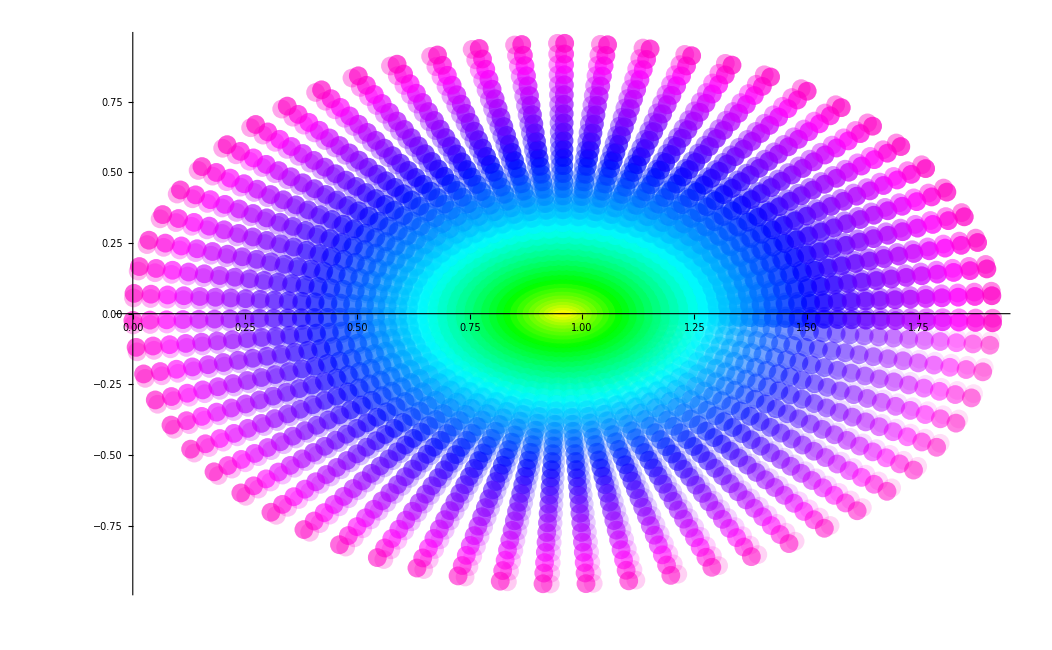

```mathematica
Show[circlemap1,PlotRange-> All]
```

```mathematica
xn[0.5,0]
```

0.9571

```mathematica
colourplotcircle2={};
Clear[x]
Clear[y]
μ = 3.8284;
xn[x_,y_] =x μ^2-x^2 μ^2+y^2 μ^2-x^2 μ^3+2 x^3 μ^3-x^4 μ^3+y^2 μ^3-6 x y^2 μ^3+6 x^2 y^2 μ^3-y^4 μ^3;
yn[x_,y_] = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
For[m=0,m<Length[listcircle],m++;
locallistcircle = {};
For[n=0,n<Length[listcircle⟦m⟧],n++;
xlocal = listcircle⟦m,n,1⟧;
ylocal = listcircle⟦m,n,2⟧;
{x1 ,y1}= {xn[xlocal,ylocal],yn[xlocal,ylocal]};
AppendTo[locallistcircle,{x1,y1}]];
AppendTo[colourplotcircle2,locallistcircle]]
```

```mathematica
Clear["Global`*"]
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))];
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]]
```

x μ^3-x^2 μ^3+y^2 μ^3-x^2 μ^4+2 x^3 μ^4-x^4 μ^4+y^2 μ^4-6 x y^2 μ^4+6 x^2 y^2 μ^4-y^4 μ^4-x^2 μ^5+2 x^3 μ^5-x^4 μ^5+y^2 μ^5-6 x y^2 μ^5+6 x^2 y^2 μ^5-y^4 μ^5+2 x^3 μ^6-6 x^4 μ^6+6 x^5 μ^6-2 x^6 μ^6-6 x y^2 μ^6+36 x^2 y^2 μ^6-60 x^3 y^2 μ^6+30 x^4 y^2 μ^6-6 y^4 μ^6+30 x y^4 μ^6-30 x^2 y^4 μ^6+2 y^6 μ^6-x^4 μ^7+4 x^5 μ^7-6 x^6 μ^7+4 x^7 μ^7-x^8 μ^7+6 x^2 y^2 μ^7-40 x^3 y^2 μ^7+90 x^4 y^2 μ^7-84 x^5 y^2 μ^7+28 x^6 y^2 μ^7-y^4 μ^7+20 x y^4 μ^7-90 x^2 y^4 μ^7+140 x^3 y^4 μ^7-70 x^4 y^4 μ^7+6 y^6 μ^7-28 x y^6 μ^7+28 x^2 y^6 μ^7-y^8 μ^7+ⅈ (y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7)

```mathematica
ComplexExpand[Normal[Series[map3[1/2+ ϵ,y,μ],{ϵ,0, 1}]]]
```

μ^3/4+y^2 μ^3-μ^4/16-(y^2 μ^4)/2-y^4 μ^4-μ^5/16-(y^2 μ^5)/2-y^4 μ^5+μ^6/32+(3 y^2 μ^6)/8+(3 y^4 μ^6)/2+2 y^6 μ^6-μ^7/256-(y^2 μ^7)/16-(3 y^4 μ^7)/8-y^6 μ^7-y^8 μ^7+ⅈ (-2 y ϵ μ^3+y ϵ μ^4+4 y^3 ϵ μ^4+y ϵ μ^5+4 y^3 ϵ μ^5-3/4 y ϵ μ^6-6 y^3 ϵ μ^6-12 y^5 ϵ μ^6+1/8 y ϵ μ^7+3/2 y^3 ϵ μ^7+6 y^5 ϵ μ^7+8 y^7 ϵ μ^7)

```mathematica
FullSimplify[(-2 y ϵ μ^3+y ϵ μ^4+4 y^3 ϵ μ^4+y ϵ μ^5+4 y^3 ϵ μ^5-3/4 y ϵ μ^6-6 y^3 ϵ μ^6-12 y^5 ϵ μ^6+1/8 y ϵ μ^7+3/2 y^3 ϵ μ^7+6 y^5 ϵ μ^7+8 y^7 ϵ μ^7)]
```

1/8 y ϵ μ^3 (-2+μ+4 y^2 μ) (8+(1+4 y^2) μ^2 (-4+μ+4 y^2 μ))

```mathematica
Normal[Series[map[1/2+ ϵ,y,μ],{ϵ,0, 1}]]
```

μ/4+y^2 μ-2 ⅈ y ϵ μ

```mathematica
ComplexExpand[Normal[Series[Series[map3[1/2+ ϵ,y,μ],{ϵ,0, 3}],{y,0,2}]]]
```

μ^3/4+y^2 μ^3-ϵ^2 μ^3-μ^4/16-(y^2 μ^4)/2+(ϵ^2 μ^4)/2+6 y^2 ϵ^2 μ^4-μ^5/16-(y^2 μ^5)/2+(ϵ^2 μ^5)/2+6 y^2 ϵ^2 μ^5+μ^6/32+(3 y^2 μ^6)/8-(3 ϵ^2 μ^6)/8-9 y^2 ϵ^2 μ^6-μ^7/256-(y^2 μ^7)/16+(ϵ^2 μ^7)/16+9/4 y^2 ϵ^2 μ^7+ⅈ (-2 y ϵ μ^3+y ϵ μ^4-4 y ϵ^3 μ^4+y ϵ μ^5-4 y ϵ^3 μ^5-3/4 y ϵ μ^6+6 y ϵ^3 μ^6+1/8 y ϵ μ^7-3/2 y ϵ^3 μ^7)

```mathematica
FullSimplify[ (-2 y ϵ μ^3+y ϵ μ^4-4 y ϵ^3 μ^4+y ϵ μ^5-4 y ϵ^3 μ^5-3/4 y ϵ μ^6+6 y ϵ^3 μ^6+1/8 y ϵ μ^7-3/2 y ϵ^3 μ^7)]
```

-1/8 y ϵ (-2+μ) μ^3 (-8-(-4+μ) μ^2+4 ϵ^2 μ (-4+3 (-2+μ) μ))

```mathematica
FullSimplify[Normal[Series[Solve[(-2+μ) μ^3 (-8-(-4+μ) μ^2+4 ϵ^2 μ (-4+3 (-2+μ) μ))== 0,μ]⟦All,1,2⟧,{ϵ,0,2}]],Assumptions->ϵ>0]
```

{0,0,0,2,-((4 √2 (5 (-533857665 ⅈ √(15 (161-72 √5))-580194727 (-9+4 √5))^(1/6)+8 √5 (-580194727 (-161+72 √5)-533857665 ⅈ √3 (-360+161 √5))^(1/6) ϵ^2))/(5 (11+3 ⅈ √15)^(2/3) (-11 ⅈ+3 √15))),1+√5+(8+24/(√5)) ϵ^2,2+8 ϵ^2}

```mathematica
1.+√5
```

3.23607

```mathematica
μ^3/4+y^2 μ^3-μ^4/16-(y^2 μ^4)/2-μ^5/16-(y^2 μ^5)/2+μ^6/32+(3 y^2 μ^6)/8-μ^7/256-(y^2 μ^7)/16/.μ-> 1.+√5
```

0.809017

```mathematica
72. √5
```

160.997

```mathematica
161. √5
```

360.007

```mathematica
Solve[(y μ-2 x y μ)== 0,x]
```

{{x→1/2}}

```mathematica
yband = {y-> 0, y-> (√(-2μ x^2+ 2μ x-1))/(√(2 μ)),  y-> -(√(-2μ x^2+ 2μ x-1))/(√(2 μ)), y-> (√(1/μ+ 6 x^2-(√(μ^3(μ^3+ 2 μ^2+μ + 32 μ^3 x^4 -64 μ^3 x^3+44 μ^3  x^2 + 8 μ^2 x^2-12 μ^3 x-8 μ^2 x-2))-6x+1)/μ^3))/(√2), y->-(√(1/μ+ 6 x^2-(√(μ^3(μ^3+ 2 μ^2+μ + 32 μ^3 x^4 -64 μ^3 x^3+44 μ^3  x^2 + 8 μ^2 x^2-12 μ^3 x-8 μ^2 x-2))-6x+1)/μ^3))/(√2)}/.{x-> 1.0, μ-> 3.8}
```

{y→0,y→0.+0.362738 ⅈ,y→0.-0.362738 ⅈ,y→1.59775,y→-1.59775}

```mathematica
Plot3D[yband⟦3,2⟧,{x,0,1},{μ,3.5,3.85}]
```

-Graphics3D-

```mathematica
map[x_,y_,μ_]= ComplexExpand[μ (x+I*y)(1-(x+I*y))]
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
map3[x_,y_,μ_]=ComplexExpand[map[Re[map2[x,y,μ]],Im[map2[x,y,μ]],μ]];
```

x μ-x^2 μ+y^2 μ+ⅈ (y μ-2 x y μ)

```mathematica
im = y μ^3-2 x y μ^3-2 x y μ^4+6 x^2 y μ^4-4 x^3 y μ^4-2 y^3 μ^4+4 x y^3 μ^4-2 x y μ^5+6 x^2 y μ^5-4 x^3 y μ^5-2 y^3 μ^5+4 x y^3 μ^5+6 x^2 y μ^6-24 x^3 y μ^6+30 x^4 y μ^6-12 x^5 y μ^6-2 y^3 μ^6+24 x y^3 μ^6-60 x^2 y^3 μ^6+40 x^3 y^3 μ^6+6 y^5 μ^6-12 x y^5 μ^6-4 x^3 y μ^7+20 x^4 y μ^7-36 x^5 y μ^7+28 x^6 y μ^7-8 x^7 y μ^7+4 x y^3 μ^7-40 x^2 y^3 μ^7+120 x^3 y^3 μ^7-140 x^4 y^3 μ^7+56 x^5 y^3 μ^7+4 y^5 μ^7-36 x y^5 μ^7+84 x^2 y^5 μ^7-56 x^3 y^5 μ^7-4 y^7 μ^7+8 x y^7 μ^7;
```

```mathematica
ys =FullSimplify[ Solve[im==0,y]]
```

{{y→0},{y→-(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→(ⅈ √(-1-2 (-1+x) x μ))/(√2 √μ)},{y→-(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→-(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)},{y→(√(1+6 (-1+x) x+1/μ+(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)}}

```mathematica
xs = Solve[im==0,x]
```

{{x→1/2},{x→(μ-√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ)},{x→(μ+√(-2 μ+μ^2+4 y^2 μ^2))/(2 μ)},{x→1/2 (1-√(1+12 y^2-2/μ-(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1+√(1+12 y^2-2/μ-(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1-√(1+12 y^2-2/μ+(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))},{x→1/2 (1+√(1+12 y^2-2/μ+(2 √(-2 μ^3+μ^4-8 y^2 μ^5+4 y^2 μ^6+32 y^4 μ^6))/μ^3))}}

```mathematica
(μs = Solve[im==0,μ]);
```

```mathematica
ContourPlot[im== 0,{x,0,1},{y,-1,1}]
```

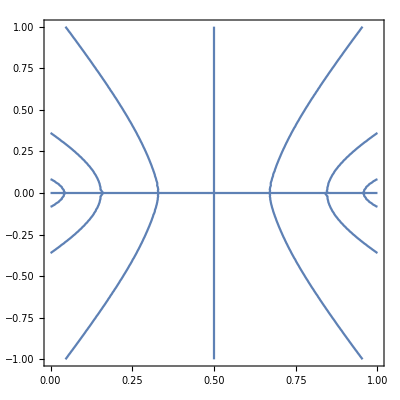

```mathematica
ContourPlot[im== 0,{x,0,1},{y,-1,1}]
```

```mathematica
Plot[ys⟦2,1,2⟧/.μ-> 3.8284,{x,0,1}]
```

-Graphics-

```mathematica
g
```

```mathematica
ComplexExpand[Normal[Series[Series[ys⟦4,1,2⟧/. x->(x+1/2),{ϵ,0, 1}],{x,0,1}]]]
```

-1/2 Cos[1/2 Arg[(2 μ^2-μ^3-2 √((-2+μ) μ^3))/μ^3]] ((-1+2/μ-(2 ((-2+μ)^2 μ^6)^(1/4) Cos[1/2 Arg[(-2+μ) μ^3]])/μ^3)^2+(4 √((-2+μ)^2 μ^6) Sin[1/2 Arg[(-2+μ) μ^3]]^2)/μ^6)^(1/4)-1/2 ⅈ ((-1+2/μ-(2 ((-2+μ)^2 μ^6)^(1/4) Cos[1/2 Arg[(-2+μ) μ^3]])/μ^3)^2+(4 √((-2+μ)^2 μ^6) Sin[1/2 Arg[(-2+μ) μ^3]]^2)/μ^6)^(1/4) Sin[1/2 Arg[(2 μ^2-μ^3-2 √((-2+μ) μ^3))/μ^3]]

```mathematica
ys
```

{{y→0},{y→-(ⅈ √(-1+2 x μ-2 x^2 μ))/(√2 √μ)},{y→(ⅈ √(-1+2 x μ-2 x^2 μ))/(√2 √μ)},{y→-(√(1-6 x+6 x^2+1/μ-(√(μ^3 (-2+μ+2 μ^2-8 x μ^2+8 x^2 μ^2+μ^3-12 x μ^3+44 x^2 μ^3-64 x^3 μ^3+32 x^4 μ^3)))/μ^3))/(√2)},{y→(√(1-6 x+6 x^2+1/μ-(√(μ^3 (-2+μ+2 μ^2-8 x μ^2+8 x^2 μ^2+μ^3-12 x μ^3+44 x^2 μ^3-64 x^3 μ^3+32 x^4 μ^3)))/μ^3))/(√2)},{y→-(√(1-6 x+6 x^2+1/μ+(√(μ^3 (-2+μ+2 μ^2-8 x μ^2+8 x^2 μ^2+μ^3-12 x μ^3+44 x^2 μ^3-64 x^3 μ^3+32 x^4 μ^3)))/μ^3))/(√2)},{y→(√(1-6 x+6 x^2+1/μ+(√(μ^3 (-2+μ+2 μ^2-8 x μ^2+8 x^2 μ^2+μ^3-12 x μ^3+44 x^2 μ^3-64 x^3 μ^3+32 x^4 μ^3)))/μ^3))/(√2)}}

```mathematica
ys⟦3,1,2⟧/. x->(x0+ϵ)
```

(0.+0.36139 ⅈ) √(-1+7.6568 (x0+ϵ)-7.6568 (x0+ϵ)^2)

```mathematica
slist = Table[ComplexExpand[Normal[Series[ys⟦i,1,2⟧/. x->(x+ϵ),{ϵ,0,1}]]],{i,1,Length[ys]}]
```

$Aborted

```mathematica
3
```

```mathematica
banda1 = FullSimplify[Normal[Series[im/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0,{ϵ,0,3}]]/ ys⟦3,1,2⟧/.x-> x0]/.μ-> 3.8284
```

214.817 ϵ (1.8284 (-1+2 x0+ϵ) (-1+2 x0+2 ϵ)+2 (3.8284-7.6568 x0)^2 ((1-2 x0)^2+7 (-1+2 x0) ϵ+18 ϵ^2)+224.446 (1-2 x0)^2 ((1-2 x0)^2 (-1+x0) x0+7 (-1+x0) x0 (-1+2 x0) ϵ+(-1+14 (-1+x0) x0) ϵ^2))

```mathematica
banda05= FullSimplify[Normal[Series[im/y,{x,1/2,8}]/.μ-> 3.8284]/.x-> 1/2+ϵ]
```

ϵ (70.3402+96429.8 y^6-3338.47 ϵ^2+34540.3 ϵ^4-96429.8 ϵ^6+y^4 (34540.3-675008. ϵ^2)+y^2 (3338.47-115134. ϵ^2+675008. ϵ^4))

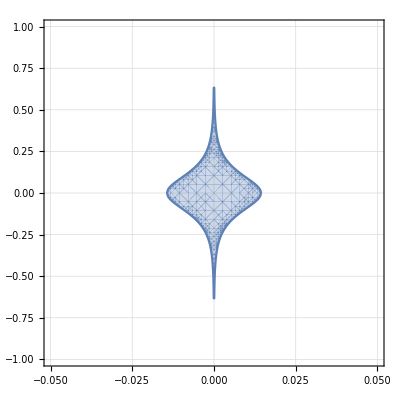

```mathematica
RegionPlot[Abs[banda05]< 1,{ϵ,-0.05,0.05},{y,-1,1},GridLines->Automatic,MaxRecursion->5]
```

```mathematica
banda312= FullSimplify[im/ys⟦3,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

Part::partd: Part specification ys⟦3,1,2⟧ is longer than depth of object.

```mathematica
banda212= FullSimplify[im/ys⟦2,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda412= FullSimplify[im/ys⟦4,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda512= FullSimplify[im/ys⟦5,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda612= FullSimplify[im/ys⟦6,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
s1 = Solve[banda1== 1,ϵ]⟦1,1,2⟧;
```

$Aborted

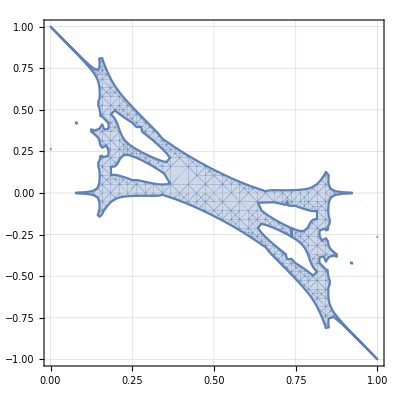

```mathematica
RegionPlot[Abs[banda612]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic]
```

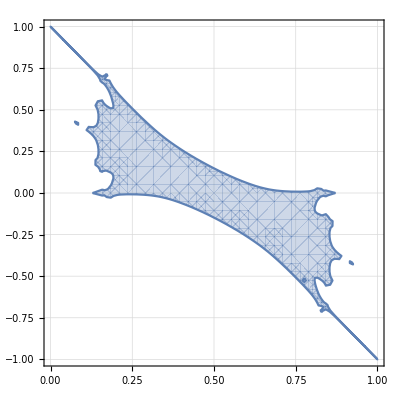

```mathematica
RegionPlot[Abs[banda512]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic]
```

```mathematica
RegionPlot[Abs[banda412]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic]
```

-Graphics-

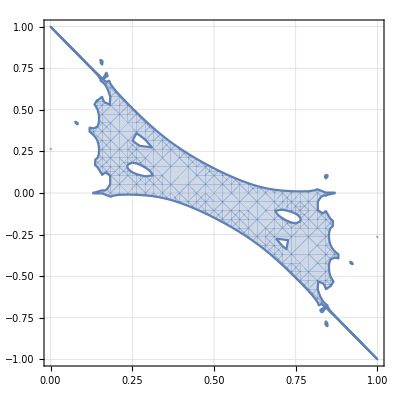

```mathematica
RegionPlot[Abs[banda212]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic]
```

```mathematica
RegionPlot[Abs[banda312]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic]
```

-Graphics-

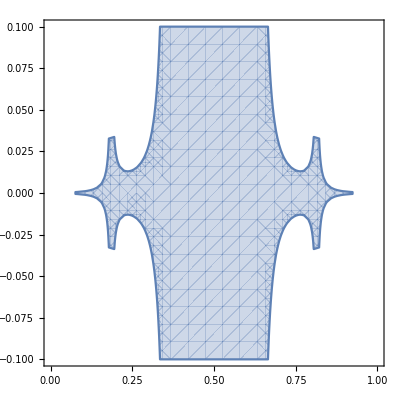

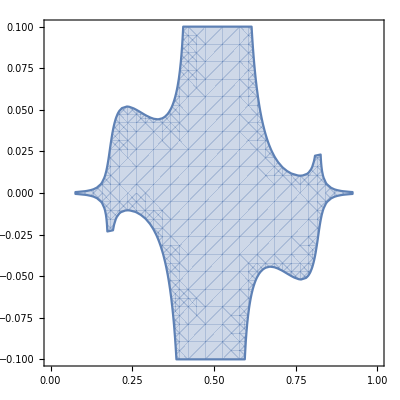

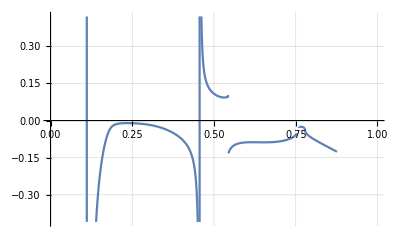

```mathematica
Plot[s1/.μ-> 3.8284,{x0,0,1},GridLines->Automatic]
```

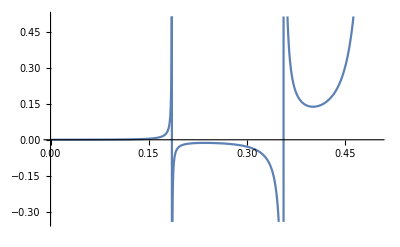

```mathematica
Region
```

```mathematica
RegionPlot[Abs[banda1]< 1,{x0,0.3,0.4},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4]}]
```

-Graphics-

```mathematica
banda1
```

ϵ (70.3402+96429.8 y^6-3338.47 ϵ^2+34540.3 ϵ^4-96429.8 ϵ^6+y^4 (34540.3-675008. ϵ^2)+y^2 (3338.47-115134. ϵ^2+675008. ϵ^4))

```mathematica
FullSimplify[(Normal[Series[im/.x-> x0+ϵ,{ϵ,0,1}]]/y)/.{y-> ys⟦2,1,2⟧,μ-> 3.8284,x-> x0}];
```

y μ^3-2 x0 y μ^3-2 x0 y μ^4+6 x0^2 y μ^4-4 x0^3 y μ^4-2 y^3 μ^4+4 x0 y^3 μ^4-2 x0 y μ^5+6 x0^2 y μ^5-4 x0^3 y μ^5-2 y^3 μ^5+4 x0 y^3 μ^5+6 x0^2 y μ^6-24 x0^3 y μ^6+30 x0^4 y μ^6-12 x0^5 y μ^6-2 y^3 μ^6+24 x0 y^3 μ^6-60 x0^2 y^3 μ^6+40 x0^3 y^3 μ^6+6 y^5 μ^6-12 x0 y^5 μ^6-4 x0^3 y μ^7+20 x0^4 y μ^7-36 x0^5 y μ^7+28 x0^6 y μ^7-8 x0^7 y μ^7+4 x0 y^3 μ^7-40 x0^2 y^3 μ^7+120 x0^3 y^3 μ^7-140 x0^4 y^3 μ^7+56 x0^5 y^3 μ^7+4 y^5 μ^7-36 x0 y^5 μ^7+84 x0^2 y^5 μ^7-56 x0^3 y^5 μ^7-4 y^7 μ^7+8 x0 y^7 μ^7+ϵ (-2 y μ^3-2 y μ^4+12 x0 y μ^4-12 x0^2 y μ^4+4 y^3 μ^4-2 y μ^5+12 x0 y μ^5-12 x0^2 y μ^5+4 y^3 μ^5+12 x0 y μ^6-72 x0^2 y μ^6+120 x0^3 y μ^6-60 x0^4 y μ^6+24 y^3 μ^6-120 x0 y^3 μ^6+120 x0^2 y^3 μ^6-12 y^5 μ^6-12 x0^2 y μ^7+80 x0^3 y μ^7-180 x0^4 y μ^7+168 x0^5 y μ^7-56 x0^6 y μ^7+4 y^3 μ^7-80 x0 y^3 μ^7+360 x0^2 y^3 μ^7-560 x0^3 y^3 μ^7+280 x0^4 y^3 μ^7-36 y^5 μ^7+168 x0 y^5 μ^7-168 x0^2 y^5 μ^7+8 y^7 μ^7)

Com isso, podemos encontrar uma região que atende essa condição, isso é, deslocamentos “ϵ” das curvas de estabilidade conhecidas que diminuem o valor de y na terceira iteração.

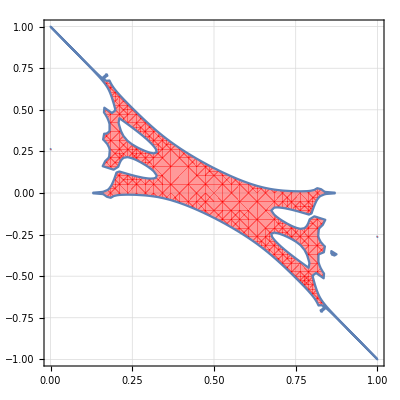

```mathematica
RegionPlot[Abs[bandaN]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4]}]
```

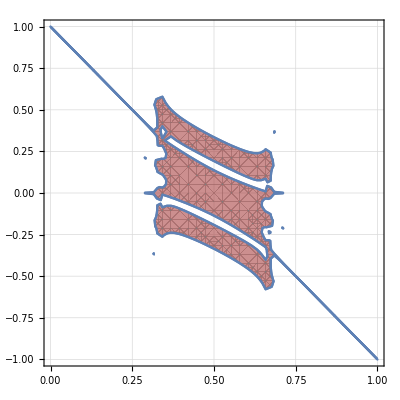

```mathematica
Show[RegionPlot[Abs[banda6]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4]}],RegionPlot[Abs[banda7]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]}]]
```

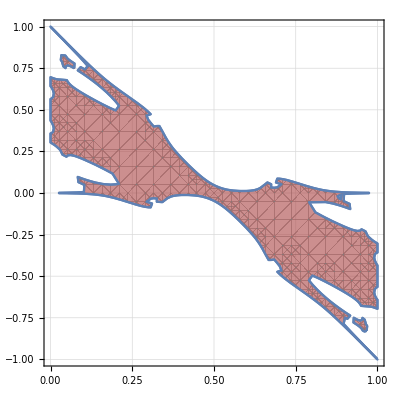

```mathematica
Show[RegionPlot[Abs[banda4]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4]}],RegionPlot[Abs[banda5]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]}]]
```

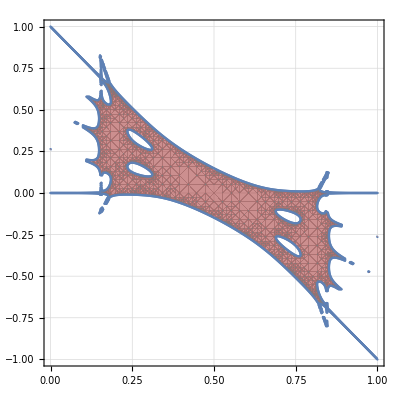

```mathematica
Show[RegionPlot[Abs[banda2]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4]},MaxRecursion->5],RegionPlot[Abs[banda3]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]},MaxRecursion->5]]
```

```mathematica
banda2
```

(214.817 √(-1-7.6568 (-1+x0) x0) ϵ (-1+2 x0+ϵ) (-1+2 x0+2 ϵ) (1.8284+29.3133 (-1+2 x0+2 ϵ)^2+224.446 (4 x0^4+x0^2 (5-12 ϵ)+8 x0^3 (-1+ϵ)-(-1+ϵ)^2 ϵ^2+x0 (-1+4 ϵ-4 ϵ^3))))/(√(-1-7.6568 (-1+x0+ϵ) (x0+ϵ)))

```mathematica
banda22= FullSimplify[(im/ys⟦2,1,2⟧/.x-> (x+ ϵ))/.y-> ys⟦2,1,2⟧/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda22
```

(214.817 √(-1-7.6568 (-1+x0) x0) ϵ (-1+2 x0+ϵ) (-1+2 x0+2 ϵ) (1.8284+29.3133 (-1+2 x0+2 ϵ)^2+224.446 (4 x0^4+x0^2 (5-12 ϵ)+8 x0^3 (-1+ϵ)-(-1+ϵ)^2 ϵ^2+x0 (-1+4 ϵ-4 ϵ^3))))/(√(-1-7.6568 (-1+x0+ϵ) (x0+ϵ)))

```mathematica
x0s = xs/.{ μ-> 3.8284}
```

{{x→1/2},{x→0.130603 (3.8284-√(6.99985+58.6266 y^2))},{x→0.130603 (3.8284+√(6.99985+58.6266 y^2))},{x→1/2 (1-√(0.477589+12 y^2-0.0356433 √(102.594+6014.75 y^2+100752. y^4)))},{x→1/2 (1+√(0.477589+12 y^2-0.0356433 √(102.594+6014.75 y^2+100752. y^4)))},{x→1/2 (1-√(0.477589+12 y^2+0.0356433 √(102.594+6014.75 y^2+100752. y^4)))},{x→1/2 (1+√(0.477589+12 y^2+0.0356433 √(102.594+6014.75 y^2+100752. y^4)))}}

```mathematica
banda2
```

(214.817 √(-1-7.6568 (-1+x0) x0) ϵ (-1+2 x0+ϵ) (-1+2 x0+2 ϵ) (1.8284+29.3133 (-1+2 x0+2 ϵ)^2+224.446 (4 x0^4+x0^2 (5-12 ϵ)+8 x0^3 (-1+ϵ)-(-1+ϵ)^2 ϵ^2+x0 (-1+4 ϵ-4 ϵ^3))))/(√(-1-7.6568 (-1+x0+ϵ) (x0+ϵ)))

1

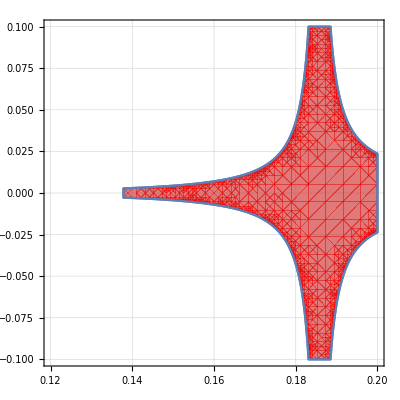

```mathematica
ordem = 1
banda2s = Normal[Series[banda2,{ϵ,0,ordem}]];
banda3s = Normal[Series[banda2,{ϵ,0,ordem}]];
Show[RegionPlot[Abs[banda2s]< 1,{x0,0.12,0.20},{ϵ,-0.1,0.1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]},MaxRecursion->5],RegionPlot[Abs[banda2s]< 1,{x0,0.12,0.20},{ϵ,-0.1,0.1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4]},MaxRecursion->5]]
```

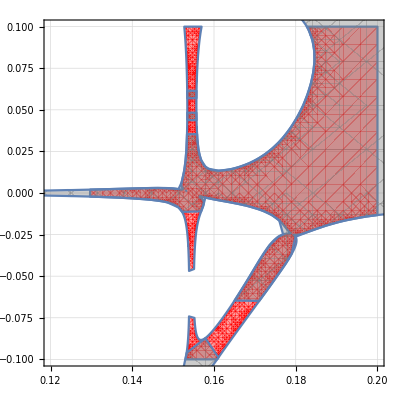

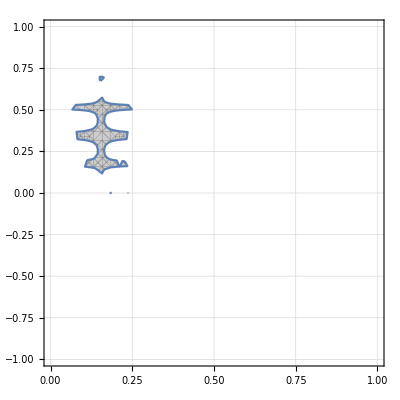

```mathematica
banda3s = Normal[Series[banda3,{x0,x0s⟦2,1,2⟧,1}]];
RegionPlot[Abs[banda3s]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]}]
```

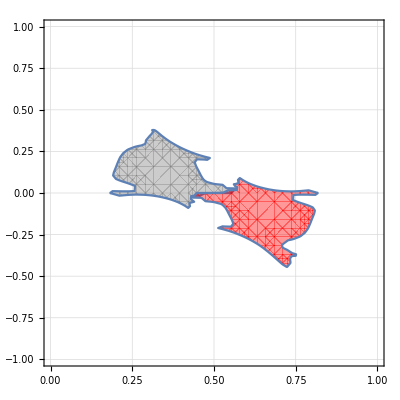

```mathematica
ordem = 4;
banda4s1 = Normal[Series[banda4,{x0,x0s⟦4,1,2⟧,ordem}]];
banda4s2 = Normal[Series[banda4,{x0,x0s⟦5,1,2⟧,ordem}]];
Show[RegionPlot[Abs[banda4s1]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]}],RegionPlot[Abs[banda4s2]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4]}]]
```

```mathematica
ordem = 4;
banda5s1 = Normal[Series[banda5,{x0,x0s⟦4,1,2⟧,ordem}]];
banda5s2 = Normal[Series[banda5,{x0,x0s⟦5,1,2⟧,ordem}]];
Show[RegionPlot[Abs[banda5s1]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]}],RegionPlot[Abs[banda5s2]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4]}]]
```

-Graphics-

```mathematica
banda6s = Normal[Series[banda7,{x0,x0s⟦6,1,2⟧,1}]];
RegionPlot[Abs[banda6s]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]}]
```

-Graphics-

```mathematica
banda3s = Normal[Series[banda2,{x0,x0s⟦2,1,2⟧,1}]];
RegionPlot[Abs[banda2s1]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]}]
```

```mathematica
x0s = xs/.{y-> 0, μ-> 3.8284};
Manipulate[
banda2s1 = Normal[Series[banda2,{x0,x0s⟦2,1,2⟧,i}]];
banda2s2 = Normal[Series[banda3,{x0,x0s⟦3,1,2⟧,i}]];
Show[RegionPlot[Abs[banda2s1]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]}],RegionPlot[Abs[banda2s2]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Red,Opacity[0.4]}]],{i,1,3,1}]
```

Part::partd: Part specification x0s⟦2,1,2⟧ is longer than depth of object.

Part::partd: Part specification x0s⟦3,1,2⟧ is longer than depth of object.

Part::partd: Part specification x0s⟦2,1,2⟧ is longer than depth of object.

Part::partd: Part specification x0s⟦3,1,2⟧ is longer than depth of object.

```mathematica
banda2
```

-(214.817 √(-1-7.6568 (-1+x0) x0) ϵ (-1+2 x0+ϵ) (-1+2 x0+2 ϵ) (1.8284+29.3133 (-1+2 x0+2 ϵ)^2+224.446 (4 x0^4+x0^2 (5-12 ϵ)+8 x0^3 (-1+ϵ)-(-1+ϵ)^2 ϵ^2+x0 (-1+4 ϵ-4 ϵ^3))))/(√(-1-7.6568 (-1+x0+ϵ) (x0+ϵ)))

```mathematica
Plot3D[banda2,{x0,0,1},{ϵ,-2,2}]
```

-Graphics3D-

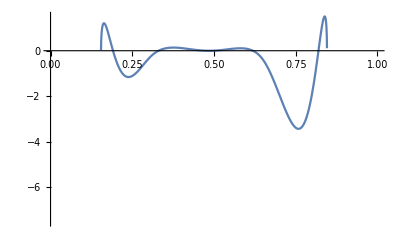

```mathematica
Plot[banda5/.ϵ-> 0.02, {x0,0,1}]
```

```mathematica
ys⟦4,1,2⟧
```

-(√(1+6 (-1+x) x+1/μ-(√(μ^3 (-2+μ+2 (1-2 x)^2 μ^2+(1-2 x)^2 (1+8 (-1+x) x) μ^3)))/μ^3))/(√2)

```mathematica
banda2s = Normal[Series[ys⟦4,1,2⟧.{x-> (x+ ϵ)}/.x-> x0,{x0,x0s⟦2,1,2⟧,5}]]
```

(2.59149 (-0.154461+x0) μ^2 √(-1/μ^3) (7+2.07402 μ √(-μ^3 (93.4278-1-1+1. μ^3))) (1.{x0→x0+ϵ}+(-0.270473 √(-(-6.83476 μ^2-1.47892 μ^3+1. √(-μ^3 (1)))/μ^3)).{0}))/((93.4278-46.7139 μ-44.62 μ^2+1. μ^3) (4.62144 μ^2+1. μ^3-0.676167 √(-μ^3 (93.4278-46.7139 μ-44.62 μ^2+1. μ^3))))+7+(-0.270473 √(-(-6.83476 μ^2-1+1. 1)/μ^3)).{x0→x0+ϵ}
 |  |  |  |

```mathematica
x0s = xs/.{y-> 0, μ-> 3.8284}
banda2s = Normal[Series[ys⟦2,1,2⟧.{x-> (x+ ϵ)}/.x-> x0,{x0,x0s⟦2,1,2⟧,5}]];
RegionPlot[Abs[banda2s]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]}]
```

{{x→1/2},{x→0.154461},{x→0.845539},{x→0.329294},{x→0.670706},{x→0.0421202},{x→0.95788}}

-Graphics-

```mathematica
RegionPlot[Abs[Normal[Series[banda2,{x0,x0s⟦2,1,2⟧,1}]]]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic]
```

General::ivar: 0.0000526842 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
banda2s=Normal[Series[banda2,{x0,x0s⟦2,1,2⟧,1}]]
```

(80163.1 √(-0.154461+1. x0) (-0.691078+ϵ) (-0.345539+ϵ) ϵ (-0.00814628+0.477589 ϵ^2-1.38216 ϵ^3+1. ϵ^4))/(√(2.89997×10^-17+0.691078 ϵ-1. ϵ^2))

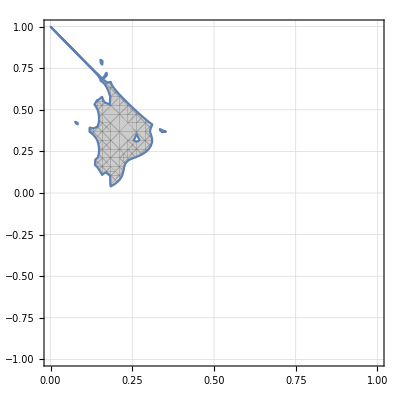

```mathematica
banda2s=Normal[Series[banda2,{x0,x0s⟦2,1,2⟧,7}]];
RegionPlot[Abs[banda2s]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]}]
```

```mathematica
x0s = xs/.{y-> 0, μ-> 3.8284}
```

{{x→1/2},{x→0.154461},{x→0.845539},{x→0.329294},{x→0.670706},{x→0.0421202},{x→0.95788}}

Podemos realizar esse mesmo tratamento para map2:

```mathematica
map2[x_,y_,μ_]=ComplexExpand[map[Re[map[x,y,μ]],Im[map[x,y,μ]],μ]];
```

```mathematica
im2 = y μ^2-2 x y μ^2-2 x y μ^3+6 x^2 y μ^3-4 x^3 y μ^3-2 y^3 μ^3+4 x y^3 μ^3;
```

```mathematica
ys2 =FullSimplify[ Solve[im2==0,y]]
```

{{y→0},{y→-(√(-1+2 x) √(1-2 x μ+2 x^2 μ))/(√(-2 μ+4 x μ))},{y→(√(-1+2 x) √(1-2 x μ+2 x^2 μ))/(√(-2 μ+4 x μ))}}

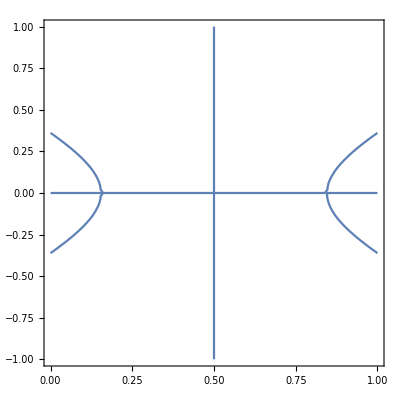

```mathematica
imμ2 =im2/.μ-> 3.8284;
ContourPlot[imμ2== 0,{x,0,1},{y,-1,1}]
```

```mathematica
banda22= FullSimplify[im/ys2⟦2,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

```mathematica
banda32= FullSimplify[im/ys2⟦3,1,2⟧/.{x-> (x+ ϵ),y-> ys⟦3,1,2⟧}/.x-> x0 ]/.μ-> 3.8284;
```

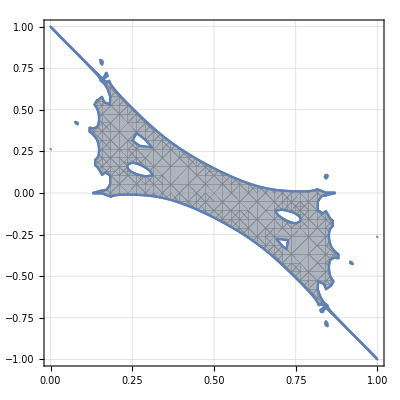

```mathematica
Show[RegionPlot[Abs[banda22]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic],RegionPlot[Abs[banda32]< 1,{x0,0,1},{ϵ,-1,1},GridLines->Automatic,PlotStyle->{Gray,Opacity[0.4]}]]
```

```mathematica
listinha = {1,2,3,4,5};
listinha[[3]]
```

3

```mathematica
sublistinha = {{1,2},{3,4}};
sublistinha[[2,1]]
```

3